```mathematica
Clear["Global`*"]

f[k_,α_] := Sum[Cos[k*m]/m^(1 + α), {m, 1, Infinity}]
```

```mathematica
kmax = With[{A = 1, α = 3}, 
  N[ArgMax[{(Abs[2(1+A^2)Zeta[1+α]-4 A^2 Zeta[1+α]-2(1+A^2)f[k,α]])(2(1+A^2)Zeta[1+α] - 2(1+A^2)f[k,α]), 0 <= k <= Pi}, k]]]//Quiet
```

NArgMax::nnum: The function value -4. Abs[f[0.143671,3.]] (4.32929-4. f[0.143671,3.]) is not a number at {k} = {0.143671}.

NArgMax[{4. Abs[f[k,3.]] (4.32929-4. f[k,3.]),0.≤k≤3.14159},k]

```mathematica
Plot[Abs[(Abs[2(1+A^2)Zeta[1+α]-4 A^2 Zeta[1+α]-2(1+A^2)f[k,α]])(2(1+A^2)Zeta[1+α] - 2(1+A^2)f[k,α])]/.{A->1,α->3},{k,-2π,2π}]
```

$Aborted

```mathematica
data = Table[{A, 
  With[{α=1}, 
   N[ArgMax[{(Abs[
         2 (1 + A^2) Zeta[1 + α] - 4 A^2  Zeta[1 + α] - 
          2 (1 + A^2) f[k, α]]) (2 (1 + A^2) Zeta[1 + α] - 
         2 (1 + A^2) f[k, α]), 0 <= k <= Pi}, k]]// Quiet]}, {A, 0, 15}]
ListLinePlot[data, Mesh -> All, Frame -> True, 
 MeshStyle -> Red, 
 FrameLabel->{Style["A",16,Bold],Rotate[Style["κ",16,Bold], -90 Degree]},
 FrameStyle->Thick,
 PlotStyle -> Blue, GridLines -> Automatic, 
 PlotRange-> {{0,16},{0,π+0.1}},
 GridLinesStyle -> LightGray,FrameLabel -> {A, "kmax"}]
```

NArgMax::nnum: The function value -Abs[3.28987-2. f[0.143671,1.]] (3.28987-2. f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -4. Abs[f[0.143671,1.]] (6.57974-4. f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.8696-10. f[0.143671,1.]] (16.4493-10. f[0.143671,1.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

{{0,NArgMax[{Abs[3.28987-2. f[k,1.]] (3.28987-2. f[k,1.]),0.≤k≤3.14159},k]},{1,NArgMax[{4. Abs[f[k,1.]] (6.57974-4. f[k,1.]),0.≤k≤3.14159},k]},{2,NArgMax[{Abs[-9.8696-10. f[k,1.]] (16.4493-10. f[k,1.]),0.≤k≤3.14159},k]},{3,NArgMax[{Abs[-26.3189-20. f[k,1.]] (32.8987-20. f[k,1.]),0.≤k≤3.14159},k]},{4,NArgMax[{Abs[-49.348-34. f[k,1.]] (55.9278-34. f[k,1.]),0.≤k≤3.14159},k]},{5,NArgMax[{Abs[-78.9568-52. f[k,1.]] (85.5366-52. f[k,1.]),0.≤k≤3.14159},k]},{6,NArgMax[{Abs[-115.145-74. f[k,1.]] (121.725-74. f[k,1.]),0.≤k≤3.14159},k]},{7,NArgMax[{Abs[-157.914-100. f[k,1.]] (164.493-100. f[k,1.]),0.≤k≤3.14159},k]},{8,NArgMax[{Abs[-207.262-130. f[k,1.]] (213.841-130. f[k,1.]),0.≤k≤3.14159},k]},{9,NArgMax[{Abs[-263.189-164. f[k,1.]] (269.769-164. f[k,1.]),0.≤k≤3.14159},k]},{10,NArgMax[{Abs[-325.697-202. f[k,1.]] (332.277-202. f[k,1.]),0.≤k≤3.14159},k]},{11,NArgMax[{Abs[-394.784-244. f[k,1.]] (401.364-244. f[k,1.]),0.≤k≤3.14159},k]},{12,NArgMax[{Abs[-470.451-290. f[k,1.]] (477.031-290. f[k,1.]),0.≤k≤3.14159},k]},{13,NArgMax[{Abs[-552.698-340. f[k,1.]] (559.278-340. f[k,1.]),0.≤k≤3.14159},k]},{14,NArgMax[{Abs[-641.524-394. f[k,1.]] (648.104-394. f[k,1.]),0.≤k≤3.14159},k]},{15,NArgMax[{Abs[-736.93-452. f[k,1.]] (743.51-452. f[k,1.]),0.≤k≤3.14159},k]}}

NArgMax::nnum: The function value -Abs[3.28987-2. f[0.143671,1.]] (3.28987-2. f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -4. Abs[f[0.143671,1.]] (6.57974-4. f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.8696-10. f[0.143671,1.]] (16.4493-10. f[0.143671,1.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

-Graphics-

```mathematica
data = Table[{A, 
  With[{α=2}, 
   N[ArgMax[{(Abs[
         2 (1 + A^2) Zeta[1 + α] - 4 A^2  Zeta[1 + α] - 
          2 (1 + A^2) f[k, α]]) (2 (1 + A^2) Zeta[1 + α] - 
         2 (1 + A^2) f[k, α]), 0 <= k <= Pi}, k]]// Quiet]}, {A, 0, 15}]
ListLinePlot[data, Mesh -> All, Frame -> True, 
 MeshStyle -> Red, 
 FrameLabel->{Style["A",16,Bold],Rotate[Style["κ",16,Bold], -90 Degree]},
 FrameStyle->Thick,
 PlotStyle -> Blue, GridLines -> Automatic, 
 PlotRange-> {{0,16},{0,π+0.1}},
 GridLinesStyle -> LightGray,FrameLabel -> {A, "kmax"}]
```

NArgMax::nnum: The function value -Abs[2.40411-2. f[0.143671,2.]] (2.40411-2. f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -4. Abs[f[0.143671,2.]] (4.80823-4. f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-7.21234-10. f[0.143671,2.]] (12.0206-10. f[0.143671,2.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

{{0,NArgMax[{Abs[2.40411-2. f[k,2.]] (2.40411-2. f[k,2.]),0.≤k≤3.14159},k]},{1,NArgMax[{4. Abs[f[k,2.]] (4.80823-4. f[k,2.]),0.≤k≤3.14159},k]},{2,NArgMax[{Abs[-7.21234-10. f[k,2.]] (12.0206-10. f[k,2.]),0.≤k≤3.14159},k]},{3,NArgMax[{Abs[-19.2329-20. f[k,2.]] (24.0411-20. f[k,2.]),0.≤k≤3.14159},k]},{4,NArgMax[{Abs[-36.0617-34. f[k,2.]] (40.8699-34. f[k,2.]),0.≤k≤3.14159},k]},{5,NArgMax[{Abs[-57.6987-52. f[k,2.]] (62.507-52. f[k,2.]),0.≤k≤3.14159},k]},{6,NArgMax[{Abs[-84.144-74. f[k,2.]] (88.9522-74. f[k,2.]),0.≤k≤3.14159},k]},{7,NArgMax[{Abs[-115.397-100. f[k,2.]] (120.206-100. f[k,2.]),0.≤k≤3.14159},k]},{8,NArgMax[{Abs[-151.459-130. f[k,2.]] (156.267-130. f[k,2.]),0.≤k≤3.14159},k]},{9,NArgMax[{Abs[-192.329-164. f[k,2.]] (197.137-164. f[k,2.]),0.≤k≤3.14159},k]},{10,NArgMax[{Abs[-238.007-202. f[k,2.]] (242.815-202. f[k,2.]),0.≤k≤3.14159},k]},{11,NArgMax[{Abs[-288.494-244. f[k,2.]] (293.302-244. f[k,2.]),0.≤k≤3.14159},k]},{12,NArgMax[{Abs[-343.788-290. f[k,2.]] (348.597-290. f[k,2.]),0.≤k≤3.14159},k]},{13,NArgMax[{Abs[-403.891-340. f[k,2.]] (408.699-340. f[k,2.]),0.≤k≤3.14159},k]},{14,NArgMax[{Abs[-468.802-394. f[k,2.]] (473.61-394. f[k,2.]),0.≤k≤3.14159},k]},{15,NArgMax[{Abs[-538.521-452. f[k,2.]] (543.33-452. f[k,2.]),0.≤k≤3.14159},k]}}

NArgMax::nnum: The function value -Abs[2.40411-2. f[0.143671,2.]] (2.40411-2. f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -4. Abs[f[0.143671,2.]] (4.80823-4. f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-7.21234-10. f[0.143671,2.]] (12.0206-10. f[0.143671,2.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

-Graphics-

```mathematica
data = Table[{α, 
  With[{A=2.3}, 
   N[ArgMax[{(Abs[
         2 (1 + A^2) Zeta[1 + α] - 4 A^2  Zeta[1 + α] - 
          2 (1 + A^2) f[k, α]]) (2 (1 + A^2) Zeta[1 + α] - 
         2 (1 + A^2) f[k, α]), 0 <= k <= Pi}, k]]// Quiet]}, {α, 1, 15}]
ListLinePlot[data, Mesh -> All, Frame -> True, 
 MeshStyle -> Red, 
 FrameLabel->{Style["α",16,Bold],Rotate[Style["κ",16,Bold], -90 Degree]},
 FrameStyle->Thick,
 PlotStyle -> Blue, GridLines -> Automatic, 
 GridLinesStyle -> LightGray,FrameLabel -> {"α", "kmax"}]
```

NArgMax::nnum: The function value -Abs[-14.1135-12.58 f[0.143671,1.]] (20.6933-12.58 f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-10.3136-12.58 f[0.143671,2.]] (15.1219-12.58 f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.28633-12.58 f[0.143671,3.]] (13.6156-12.58 f[0.143671,3.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

{{1,NArgMax[{Abs[-14.1135-12.58 f[k,1.]] (20.6933-12.58 f[k,1.]),0.≤k≤3.14159},k]},{2,NArgMax[{Abs[-10.3136-12.58 f[k,2.]] (15.1219-12.58 f[k,2.]),0.≤k≤3.14159},k]},{3,NArgMax[{Abs[-9.28633-12.58 f[k,3.]] (13.6156-12.58 f[k,3.]),0.≤k≤3.14159},k]},{4,NArgMax[{Abs[-8.89684-12.58 f[k,4.]] (13.0446-12.58 f[k,4.]),0.≤k≤3.14159},k]},{5,NArgMax[{Abs[-8.7288-12.58 f[k,5.]] (12.7982-12.58 f[k,5.]),0.≤k≤3.14159},k]},{6,NArgMax[{Abs[-8.65164-12.58 f[k,6.]] (12.685-12.58 f[k,6.]),0.≤k≤3.14159},k]},{7,NArgMax[{Abs[-8.61498-12.58 f[k,7.]] (12.6313-12.58 f[k,7.]),0.≤k≤3.14159},k]},{8,NArgMax[{Abs[-8.59723-12.58 f[k,8.]] (12.6053-12.58 f[k,8.]),0.≤k≤3.14159},k]},{9,NArgMax[{Abs[-8.58853-12.58 f[k,9.]] (12.5925-12.58 f[k,9.]),0.≤k≤3.14159},k]},{10,NArgMax[{Abs[-8.58424-12.58 f[k,10.]] (12.5862-12.58 f[k,10.]),0.≤k≤3.14159},k]},{11,NArgMax[{Abs[-8.58211-12.58 f[k,11.]] (12.5831-12.58 f[k,11.]),0.≤k≤3.14159},k]},{12,NArgMax[{Abs[-8.58105-12.58 f[k,12.]] (12.5815-12.58 f[k,12.]),0.≤k≤3.14159},k]},{13,NArgMax[{Abs[-8.58053-12.58 f[k,13.]] (12.5808-12.58 f[k,13.]),0.≤k≤3.14159},k]},{14,NArgMax[{Abs[-8.58026-12.58 f[k,14.]] (12.5804-12.58 f[k,14.]),0.≤k≤3.14159},k]},{15,NArgMax[{Abs[-8.58013-12.58 f[k,15.]] (12.5802-12.58 f[k,15.]),0.≤k≤3.14159},k]}}

NArgMax::nnum: The function value -Abs[-14.1135-12.58 f[0.143671,1.]] (20.6933-12.58 f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-10.3136-12.58 f[0.143671,2.]] (15.1219-12.58 f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.28633-12.58 f[0.143671,3.]] (13.6156-12.58 f[0.143671,3.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

-Graphics-

```mathematica
data = Table[{α, 
  With[{A=2.3}, 
   N[ArgMax[{(Abs[
         2 (1 + A^2) Zeta[1 + α] - 4 A^2  Zeta[1 + α] - 
          2 (1 + A^2) f[k, α]]) (2 (1 + A^2) Zeta[1 + α] - 
         2 (1 + A^2) f[k, α]), 0 <= k <= Pi}, k]]// Quiet]}, {α, 1, 15}]
ListLinePlot[data, Mesh -> All, Frame -> True, 
 MeshStyle -> Red, 
 FrameLabel->{Style["α",16,Bold],Rotate[Style["κ",16,Bold], -90 Degree]},
 FrameStyle->Thick,
 PlotStyle -> Blue, GridLines -> Automatic, 
 GridLinesStyle -> LightGray,FrameLabel -> {"α", "kmax"}]
```

NArgMax::nnum: The function value -Abs[-14.1135-12.58 f[0.143671,1.]] (20.6933-12.58 f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-10.3136-12.58 f[0.143671,2.]] (15.1219-12.58 f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.28633-12.58 f[0.143671,3.]] (13.6156-12.58 f[0.143671,3.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

{{1,NArgMax[{Abs[-14.1135-12.58 f[k,1.]] (20.6933-12.58 f[k,1.]),0.≤k≤3.14159},k]},{2,NArgMax[{Abs[-10.3136-12.58 f[k,2.]] (15.1219-12.58 f[k,2.]),0.≤k≤3.14159},k]},{3,NArgMax[{Abs[-9.28633-12.58 f[k,3.]] (13.6156-12.58 f[k,3.]),0.≤k≤3.14159},k]},{4,NArgMax[{Abs[-8.89684-12.58 f[k,4.]] (13.0446-12.58 f[k,4.]),0.≤k≤3.14159},k]},{5,NArgMax[{Abs[-8.7288-12.58 f[k,5.]] (12.7982-12.58 f[k,5.]),0.≤k≤3.14159},k]},{6,NArgMax[{Abs[-8.65164-12.58 f[k,6.]] (12.685-12.58 f[k,6.]),0.≤k≤3.14159},k]},{7,NArgMax[{Abs[-8.61498-12.58 f[k,7.]] (12.6313-12.58 f[k,7.]),0.≤k≤3.14159},k]},{8,NArgMax[{Abs[-8.59723-12.58 f[k,8.]] (12.6053-12.58 f[k,8.]),0.≤k≤3.14159},k]},{9,NArgMax[{Abs[-8.58853-12.58 f[k,9.]] (12.5925-12.58 f[k,9.]),0.≤k≤3.14159},k]},{10,NArgMax[{Abs[-8.58424-12.58 f[k,10.]] (12.5862-12.58 f[k,10.]),0.≤k≤3.14159},k]},{11,NArgMax[{Abs[-8.58211-12.58 f[k,11.]] (12.5831-12.58 f[k,11.]),0.≤k≤3.14159},k]},{12,NArgMax[{Abs[-8.58105-12.58 f[k,12.]] (12.5815-12.58 f[k,12.]),0.≤k≤3.14159},k]},{13,NArgMax[{Abs[-8.58053-12.58 f[k,13.]] (12.5808-12.58 f[k,13.]),0.≤k≤3.14159},k]},{14,NArgMax[{Abs[-8.58026-12.58 f[k,14.]] (12.5804-12.58 f[k,14.]),0.≤k≤3.14159},k]},{15,NArgMax[{Abs[-8.58013-12.58 f[k,15.]] (12.5802-12.58 f[k,15.]),0.≤k≤3.14159},k]}}

NArgMax::nnum: The function value -Abs[-14.1135-12.58 f[0.143671,1.]] (20.6933-12.58 f[0.143671,1.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-10.3136-12.58 f[0.143671,2.]] (15.1219-12.58 f[0.143671,2.]) is not a number at {k} = {0.143671}.

NArgMax::nnum: The function value -Abs[-9.28633-12.58 f[0.143671,3.]] (13.6156-12.58 f[0.143671,3.]) is not a number at {k} = {0.143671}.

General::stop: Further output of NArgMax::nnum will be suppressed during this calculation.

-Graphics-

For the AL gain maximization:

```mathematica
data = Table[{A, 
 N[ArgMax[{(Abs[2(1+A^2)(1-Cos[k])- 2 A^2])(2(1+A^2)(1-Cos[k])), 0 <= k <= Pi,k}]]// Quiet}, {A, 0, 15}],
 ListLinePlot[data, Mesh -> All, Frame -> True, 
 MeshStyle -> Red, 
 FrameLabel->{Style["A",16,Bold],Rotate[Style["κ",16,Bold], -90 Degree]},
 FrameStyle->Thick,
 PlotStyle -> Blue, GridLines -> Automatic, 
 PlotRange-> {{0,16},{0,π+0.1}},
 GridLinesStyle -> LightGray,FrameLabel -> {A, "kmax"}]
```

```mathematica
g[k_,A_,α_]:=Sqrt[Abs[2(1+A^2)Zeta[1+α]-4 A^2 Zeta[1+α]-2(1+A^2)f[k,α]]*(2(1+A^2)Zeta[1+α] - 2(1+A^2)f[k,α])]
```

```mathematica
Rasterize[ContourPlot[g[k,A,α]/.{α->1},{k,-π,π},{A,0,4},PlotLegends->Automatic]]
```

```mathematica
Rasterize[ContourPlot[g[k,A,α]/.{α->5},{k,-π,π},{A,0,4},PlotLegends->Automatic]]
```

```mathematica
ContourPlot[g[k,A,α]/.{α->0.5},{k,-π,π},{A,0,10},PlotLegends->Automatic]
```

```mathematica
Cos[π]
```

-1

```mathematica
Cos[2π]
```

1

```mathematica
Cos[3π]
```

-1

```mathematica
Cos[3 π/2]
```

0

```mathematica
π/2+π/2+π/2
```

(3 π)/2

```mathematica
Cos[2π]
```

1

```mathematica
F[a_,b_]:=Cos[m*a/b π]
```

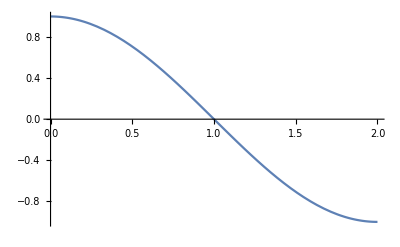

```mathematica
With[{a=1,b=2},Plot[F[a,b],{m,0,2*a}]]
```

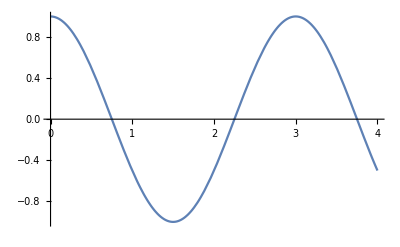

```mathematica
With[{a=2,b=3},Plot[F[a,b],{m,0,2a}]]
```